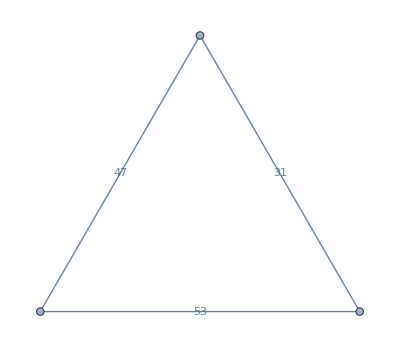

```mathematica
g=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,1]},EdgeCost->{1,3,-2},EdgeWeight->RandomInteger[54,3],EdgeLabels->"EdgeWeight"]
```

```mathematica
FindMinimumCostFlow[g,1,3]
```

2

```mathematica
EvenMixedGraphAlgorithm[g_?MixedGraphQ]:=Block[{arcs,edges},arcs=EdgeList[g,_->_];edges=EdgeList[g,_<->_];]
```

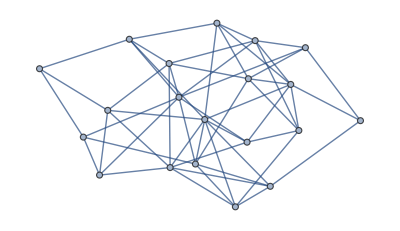

```mathematica
RandomGraph[{20,54}]
```